```mathematica
ClearAll["Global`*"];
```

```mathematica
coords1 = {t,r,θ,ϕ};
n=Length[coords1];
tt=-f0[r,θ]* H[r]+ f2[r,θ]*r^2*Sin[θ]^2W[r,θ]^2;
rr=f1[r,θ]/H[r] ;
θθ=f1[r,θ]*r^2;
ϕϕ=f2[r,θ]* r^2*Sin[θ]^2;
tϕ=-f2[r,θ]*r^2*Sin[θ]^2W[r,θ];
metric1={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric1//MatrixForm;
inversemetric1=Simplify[Inverse[metric1]];
inversemetric1 //MatrixForm;
Rtor[R_] := R - a^2/rplus;
```

```mathematica
coords2 = {t,R,θ,ϕ};
n=Length[coords2];
tt=2 M R/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M R (R^2+a^2))/ρ)Sin[θ]^2;
tϕ=-4 a M R Sin[θ]^2/ρ;
metric2={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric2//MatrixForm;
inversemetric2=Simplify[Inverse[metric2]];
inversemetric2 //MatrixForm;
a=.;M=.;
ρ=R^2+a^2 Cos[θ]^2;
Δ=R^2 - 2 M R+ a^2;
M = (rh-2 ct)/2;
a = Sqrt[ct(ct-rh)];
rplus = M+Sqrt[M^2-a^2];
```

```mathematica
f0[r_,t_]:=  1/f2[r,t]
```

```mathematica
christoffel1:=christoffel1=Simplify[Table[(1/2)*Sum[(inversemetric1[[i,s]])*
(D[metric1[[s,j]],coords1[[k]] ]+
D[metric1[[s,k]],coords1[[j]] ]-D[metric1[[j,k]],coords1[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel1:=Table[If[UnsameQ[christoffel1[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel1[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic1:=geodesic1=Simplify[Table[-Sum[christoffel1[[i,j,k]]coords1[[j]]' coords1[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic1:=Table[{"d/dτ"ToString[coords1[[i]]'],"=",geodesic1[[i]]},{i,1,n}]
geodesic1:=geodesic1=Simplify[Table[-Sum[christoffel1[[i,j,k]]coords1[[j]]' coords1[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
christoffel2:=christoffel2=Simplify[Table[(1/2)*Sum[(inversemetric2[[i,s]])*
(D[metric2[[s,j]],coords2[[k]] ]+
D[metric2[[s,k]],coords2[[j]] ]-D[metric2[[j,k]],coords2[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel2:=Table[If[UnsameQ[christoffel2[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel2[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic2:=geodesic2=Simplify[Table[-Sum[christoffel2[[i,j,k]]coords2[[j]]' coords2[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic2:=Table[{"d/dτ"ToString[coords2[[i]]'],"=",geodesic2[[i]]},{i,1,n}]
geodesic2:=geodesic2=Simplify[Table[-Sum[christoffel2[[i,j,k]]coords2[[j]]' coords2[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
H[r_]:=1-rh/r;
f1[r_,θ_]:=   (1-ct/r)^2+(ct (ct-rh) Cos[θ]^2)/r^2   ;
f2[r_,θ_]:=  1/((1-ct/r)^2+(ct (ct-rh) Cos[θ]^2)/r^2)(( (1-ct/r)^2+ (ct (ct-rh))/r^2)^2 +ct (rh-ct)(1-rh/r) Sin[θ]^2/r^2);

W[r_,θ_]:=  (1-ct/r)/r^3(√(ct (ct-rh))(rh-2 ct))/(( (1-ct/r)^2+ (ct (ct-rh))/r^2)^2 +ct (rh-ct)(1-rh/r) Sin[θ]^2/r^2);
```

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. 
it calculates whether the trajectory is timelike or null from the variable χ and uinvar which is determined before 
calling the function *)
computeSoln1[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric1;
tmp=tmp/.Table[coords1[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords1[[i]]''[τ]==(geodesic1[[i]]/.Join[Table[coords1[[i]]'->coords1[[i]]'[τ],{i,1,n}],Table[coords1[[i]]->coords1[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords1[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords1[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords1,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(Re[r[τ]]≤1.01*rh),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
computeSoln2[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric2;
tmp=tmp/.Table[coords2[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords2[[i]]''[τ]==(geodesic2[[i]]/.Join[Table[coords2[[i]]'->coords2[[i]]'[τ],{i,1,n}],Table[coords2[[i]]->coords2[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords2[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords2[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords2,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(Re[R[τ]]≤1.01*rplus),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler *)
sphslnToCartsln1[soln_]:=Block[{xs,ys,zs},xs=(r[τ]+a^2/rplus) Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=(r[τ]+a^2/rplus) Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=(r[τ]+a^2/rplus) Cos[θ[τ]]/.soln;{xs,ys,zs}]
sphslnToCartsln2[soln_]:=Block[{xs,ys,zs},xs=R[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=R[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=R[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
coordlist1[τin_,soln_]:=Table[ToString[coords1[[i]]]<>" = "<>{ToString[coords1[[i]][τin]/.soln//First]},{i,1,n}]
coordlist2[τin_,soln_]:=Table[ToString[coords2[[i]]]<>" = "<>{ToString[coords2[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
genXYPlot1[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln1 = computeSoln1[mτ,ivsin,icsin];
xyz=sphslnToCartsln1[soln1];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist1[τend,soln1]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot1[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln1 = computeSoln1[mτ,ivsin,icsin];
xyz=sphslnToCartsln1[soln1];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist1[τend,soln1]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot1[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln1 = computeSoln1[mτ,ivsin,icsin];
xyz=sphslnToCartsln1[soln1];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist1[τend,soln1]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot1[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln1 = computeSoln1[mτ,ivsin,icsin];
xyz=sphslnToCartsln1[soln1];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist1[τend,soln1]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYPlot2[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln2 = computeSoln2[mτ,ivsin,icsin];
xyz=sphslnToCartsln2[soln2];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist2[τend,soln2]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot2[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln2 = computeSoln2[mτ,ivsin,icsin];
xyz=sphslnToCartsln2[soln2];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist2[τend,soln2]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot2[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln2 = computeSoln2[mτ,ivsin,icsin];
xyz=sphslnToCartsln2[soln2];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist2[τend,soln2]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot2[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln2 = computeSoln2[mτ,ivsin,icsin];
xyz=sphslnToCartsln2[soln2];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist2[τend,soln2]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

1.

1.5

For initial coordinates={0,5.5,π/2,π/4} and initial velocities={-0.1,0,0.001} the particle crosses the horizon at τend=42.5686

With final coordinates={t = 20.9592 + 0. I,r = 1.01 + 0. I,θ = 1.5708 + 0. I,ϕ = 4.22898 + 0. I}

For initial coordinates={0,6,π/2,π/4} and initial velocities={-0.1,0,0.001} the particle crosses the horizon at τend=54.7682

With final coordinates={t = 10.0785 + 0. I,R = 1.515 + 0. I,θ = 1.5708 + 0. I,ϕ = 2.23077 + 0. I}

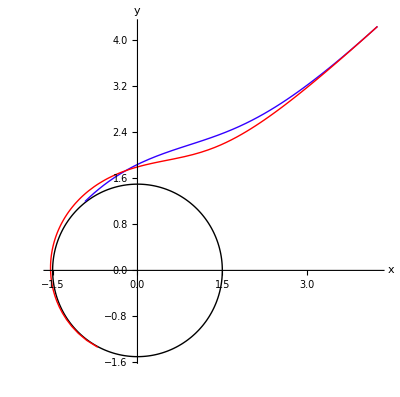

```mathematica
τend=.;uinvar = 0;
(*M=1;a=0.99;
rh=M+Sqrt[M^2-a^2];ct=rh/2-1;*)
rh=1; ct=-0.5;
rplus-a^2/rplus
rplus
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot1=50;
τPlot2=55;
(* first one, in red, is other Kerr and the second one, in blue, is BL Kerr *)
genXYPlot1[τPlot1,{0,Rtor[6 rh],π/2,π/4},{-0.1,0,0.001},1];
genXYPlot2[τPlot2,{0,6rh,π/2,π/4},{-0.1,0,0.001},0.7];
Show[horizpl,%,%%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y}]
```

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.002} the particle crosses the horizon at τend=69.636

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.0015} the particle crosses the horizon at τend=69.4991

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.001} the particle crosses the horizon at τend=69.5791

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.0005} the particle crosses the horizon at τend=69.8839

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.} the particle crosses the horizon at τend=70.4351

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.0005} the particle crosses the horizon at τend=71.2731

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.001} the particle crosses the horizon at τend=72.4678

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.0015} the particle crosses the horizon at τend=74.1454

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.002} the particle crosses the horizon at τend=76.5553

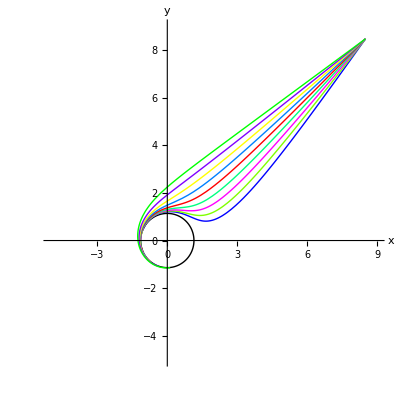

```mathematica
τend=.;uinvar = 0;
rh=1+Sqrt[1-0.99^2];ct=rh/2-1;
horizpl=PolarPlot[rh,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=150;
Table[genXYPlot1[τPlot,{0,12,π/2,π/4},{-0.15,0,0+i*0.001},1-i*(5/6)],{i,-2,2,0.5}];
Table[genXYPlot2[τPlot,{0,12,π/2,π/4},{-0.15,0,0+i*0.001},1-i*(5/6)],{i,-2,2,0.5}];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-5,9},{-5,9}}]
```

```mathematica
τend=.;uinvar = 0;
rh=1+Sqrt[1-0.99^2];ct=rh/2-1;
ivs={-0.15,0.01,0.017};ics={0,10,π/3,Pi/4};
horizpl=SphericalPlot3D[{rh,EdgeForm[]},{θ,0,Pi},{ϕ,0, 2Pi},DisplayFunction->Identity,PlotPoints->50];
τPlot = 300;
Table[genXYZPlot[τPlot,{0,10,π/3,π/4},{-0.05,0.001,0+i*0.001},1-i*(5/6)],{i,-2,2,1}];
Show[%,horizpl]
```

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,-0.002} the particle crosses the horizon at τend=181.812

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,-0.001} the particle crosses the horizon at τend=174.859

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,0.} the particle crosses the horizon at τend=177.538

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,0.001} the particle crosses the horizon at τend=194.52

The particle did not cross the horizon for initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,0.002}

-Graphics3D-

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.00146} the particle crosses the horizon at τend=73.9888

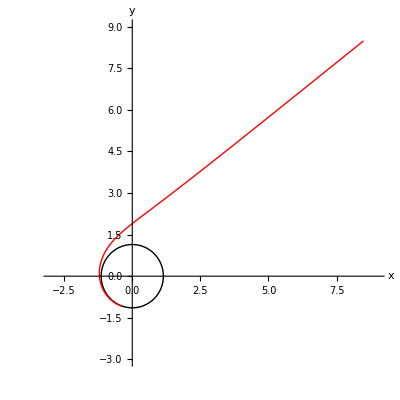

```mathematica
τend=.;uinvar = 0;
rh=1+Sqrt[1-0.99^2];ct=rh/2-1;
horizpl=PolarPlot[rh,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=190;
genXYPlot[τPlot,{0,12,π/2,π/4},{-0.15,0,0.00146},1];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-3,9},{-3,9}}]
```

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.0012728} the particle crosses the horizon at τend=73.3116

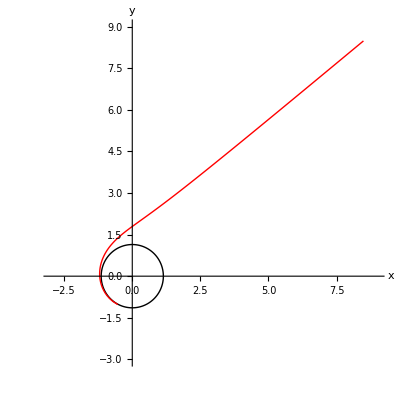

```mathematica
τend=.;uinvar = 0;
rh=1+Sqrt[1-0.99^2];ct=rh/2-1;
horizpl=PolarPlot[rh,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=190;
genXYPlot[τPlot,{0,12,π/2,π/4},{-0.15,0,0.0012728},1];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-3,9},{-3,9}}]
```